# Physics through Computational Thinking

## Periodic Motion and Dynamics

Auditya Sharma and Ambar Jain

Dept. of Physics, IISER Bhopal

Outline

In this lecture you will

1. review oscillatory motion

### Simple Harmonic Oscillator

A simple harmonic oscillator is a dynamical system that obeys the following equation of motion:

x^(..)+ω^2 x=0

Solution of this equation is given by

x(t)=A cos(ω t)+B sin(ω t)

It is easy to check explicitly that this is a solution of eqn. (1).  A and B are integration constants. We require boundary conditions or initial value condition t find them.

The solution can be written alternatively in the following forms:

x(t)=C ⅇ^(ⅈ ω t)+D ⅇ^(-ⅈ ω t)
x(t)=F cos(ω t+ϕ)
x(t)=G sin(ω t+ψ)

Here A, D etc. represent integration constants. As a homework, verify that all of the above equations satisfy eqn. (1).

These solutions represent sinusoidal oscillatory motion. We can plot these solutions and verify

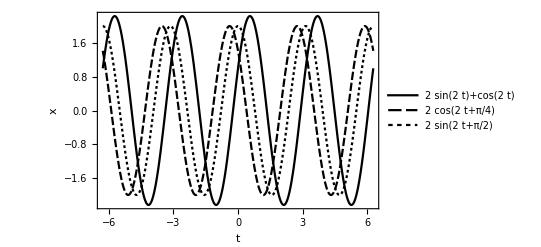

```mathematica
Plot[{2 Sin[2 t]+Cos[2t],2Cos[2t+π/4],2Sin[2t+π/2]},{t,-2π,2π},PlotLegends->"Expressions",Frame->True,FrameLabel->{"t","x"}]
```

It is easy to see from the plots of the graphs that ω is the angular frequency which has units of radians per second. ω measures periodicity of oscillatory motion.

Inverse of ω gives the time period

T=(2π)/ω

Frequency ν, also defined as number of cycles per unit time is related to ω and T as

ν=1/T
ν=ω/(2π)

Phase, Frequency, Time period and Amplitude: The solution in the form A cos(ω t+ϕ) is particularly instructive. A represents the amplitude, ω is frequency and ϕ is phase shift. Lets explore the effects of these constants using Manipulate:

x(t)=A cos(ω t+ϕ)

```mathematica
Manipulate[Plot[A Cos[ω t+ϕ],{t,-2π,2π},Frame->True,PlotRange->{-5,5},PlotLabel->Row[{"A =",A,"; ω =",ω,"; ϕ =",ϕ}]],{{A,2},0.1,5,0.1},{{ω,1},0.1,5,0.1},{{ϕ,π/4},-π,π,π/16}]
```

Aside: For labelling the above plot I have use Row function to create a row of mixed expressions such as Text, Numbers and Fractions. This comes in quite handy if you want to put in important information on your plot where you require both text and arbitrary mathematical expressions.

```mathematica
Row[{"A=",1,"; ω=",2,"; ϕ=",π/4}]
```

A=1; ω=2; ϕ=π/4

### Examples of Simple Harmonic Oscillators Example -1: Longitudinal Oscillations in a Spring and Mass system

-Graphics-

Consider the spring and mass system shown in the figure above, where each of the spring has spring constant k and natural length a_0. z is the displacement from the equilibrium position shown in the middle figure. We obtain the equation of motion of the system

m z^(..)=-k(a+z-a_0)+k(a-z-a_0)
m z^(..)=-2k z
z^(..)=-(2k)/m z

This is an equation of a simple harmonic oscillator with

ω^2=(2k)/m
ω=√(2k/m).

The potential for this system is given by

V(z)=1/2(k(a+z-a_0))^2+1/2(k(a-z-a_0))^2

You can verify easily that equation of motion given in eqn. (7) is equivalent to

m z^(..)=-ⅆ/ⅆz V(z)

Working with potentials is often easier to obtain equations of motion.

### Example -2: Pendulum

-Graphics-

For a simple pendulum, the equation of motion is given by

m ℓ^2 θ^(..)=-m g ℓ sin θ
⇒θ^(..)=-g/ℓ sin θ

For small angular displacement θ, sin θ can be approximated as θ, therefore the equation of motion simplifies to

θ^(..)=-g/ℓ θ
⇒ θ^(..)+g/ℓ θ=0

Which has the form of  SHO with ω^2=g/ℓ or ω=√(g/ℓ).

We can also examine this potential from the perspective of its potential. Potential energy is given by

V(θ)=m g ℓ(1-cos θ)
⇒V(θ)≃(m g ℓ)/2 θ^2

Since for the small angle approximation, potential has the quadratic form, we expect simple harmonic motion for small deviation from the mean position.

### Example -3: LC Circuits

-Graphics-

Lets consider the LC circuit as shown in the figure above.  Let us take capacitor to be full charged when switch S is closed. At this time current starts flowing through the circuit and capacitor starts to discharge. As the current increases the potential across the inductor starts to build up. At all times the potential across the capacitor and the inductor is equal and opposite.

We will use this to find the dynamical equation of the system for this system.

Potential across the inductor is given by: L ⅆI/ⅆt

Potential across the capacitor is given by: Q/C

Using the fact that total potential in the LC circuit is zero (Kirchhoffs law) we have

L ⅆI/ⅆt+Q/C=0

Using I=ⅆQ/ⅆt, we get

L (ⅆ^2 Q)/(ⅆ t^2)+Q/C=0
⇒Q^(..)+1/(L C)Q=0

This has the form of SHO where Q is the dynamical variable and frequency is given by

ω=√(1/(L C))

It is well-known that LC circuits oscillate with resonance frequency √(1/L C).

We can also obtain the potential of this circuit

V(Q)=Q^2/(2C)+1/2 L I^2=0

Taking the derivative of the above equation also gives us eqn. (13). Verify this as homework.

### Boundary Value Problem: LC Circuits

For the  LC circuit if the capacitor has charge Q_0 at the time t=0, when the switch S is turned on, find the charge across the capacitor as a function of time and the current in the circuit as a function of time. Show that the charge and the current are have a phase separation of π/2, that is they are out of phase. Plot the charge and the current on the same plot to demonstrate the phase shift.

### Solution

Solution: Equation of motion is given by

Q^(..)+1/(L C)Q=0

The most general solution is given by

Q(t)=A cos(ω t+ϕ)

where ω=1/√(L C). We need to determine A and ϕ, two integration constants. For this we will use the following initial conditions that hold at t=0:

Q(0)=Q_0 |     ⇒     | Q_0=A cosϕ
Q̇(0)=0 |    ⇒    | 0=-A ω sinϕ

Solving the two equations for a non-trivial solution, we get

ϕ=0
A=Q_0

Thus our solution for charge and current are

Q(t)=Q_0 cosωt
I(t)=Q_0 ω sin ωt=Q_0 ω cos(ω t-π/2)

There is a phase difference between the charge and the current. We say that the current is lagging the charge by a phase of π/2.

We can suitably non-dimensionalize the current and charge and plot it with respect to ω t which is a dimensionless measure of time. Its evident from the plot that current as a function of time has the same shape as the charge, except that it lags by π/2.

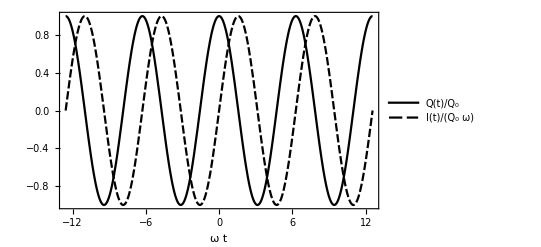

```mathematica
Plot[{Cos[t],Sin[t]},{t,-4π,4π},Frame->True,PlotLegends->{"Q(t)/Q_0","I(t)/(Q_0 ω)"},FrameLabel->{"ω t",""}]
```

Homework: As a homework exercise calculate and plot the energy contained in the capacitor and the inductor as a function of time. What is the average energy contained in the capacitor and inductor per cycle?

### Anharmonic Oscillator

-Graphics-

Let us consider the pendulum again, but this time we will assume that our angle is small but not small enough to make a linear approximation: sin θ≃θ. This can happen even when you are making small angle deviations but you are making very precise measurements such that the linear approximation for sin θ does not hold. In such a case you will Taylor expand sin θ to next order. This gives

θ^(..)=-g/ℓ sin θ
⇒θ^(..)=-g/ℓ(θ-θ^3/6)

This is an example of an anharmonic oscillator. Appearance of linear term in dynamical variable with negative sign in the force is signature of restoring force, thus oscillatory motion. Appearance of a non-linear term in the force is signature of anharmonicity in the oscillator. This essentially means that the motion will be oscillatory but it would not be sinusoidal in nature.

In general, analytical solutions of anharmonic oscillator are very few and difficult to find. We will need to solve them numerically.

We can also detect the anharmonicity in the potential. Expanding the potential to the next order we have

V(θ)=m g ℓ(1-cos θ)
⇒V(θ)≃m g ℓ (θ^2/2-θ^4/24)

Appearance of powers higher than two in the series expansion of the potential is sign of anharmonicity. Truncation of the expansion depends upon the accuracy of the theoretical results that we require and experimental accuracy of the experiment.

### Homework

1. Consider the following ways of writing the solution of the simple harmonic oscillator.

x(t)=A cos(ω t)+B sin(ω t)
x(t)=C ⅇ^(ⅈ ω t)+D ⅇ^(-ⅈ ω t)
x(t)=F cos(ω t+ϕ)
x(t)=G sin(ω t+ψ)

Find C, D, F, G, ϕ and ψ in terms of A and B.

2. Transverse Oscillations in Spring System: (a) For the spring mass system shown below, where the motion of the mass is constraint along y-axis, show that for the small oscillations the system is a simple harmonic oscillator. Take the spring constant of each spring to be k and natural length of each spring to be a_0. Find the frequency of oscillation and the time period.

-Graphics-

(b) Find the ratio of frequencies for the longitudinal oscillations we obtained in the class to transverse oscillation you obtained in this problem.

3. (a) Show that the solution of the exact pendulum equation

θ^(..)=-g/ℓ sin θ

can be written in the form of the following indefinite integral:

t=∫ⅆθ 1/(√(A-ω^2 cos θ))

where A is an integration constant. The other integration constant will emerge from performing the indefinite integral, thus it is hidden in the integral. Interpret A, that is, what is physical meaning of the constant A in this expression.

(b) Derive the solution of the form of eqn. (2) or (3) by making small angle approximation in eqn. (27).